```mathematica
ClearAll["Global`*"]
SetDirectory[NotebookDirectory[]];SetOptions[$FrontEndSession,NotebookAutoSave->True];
NotebookSave[];
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"Dropbox","EpidCRNmodels"}]];<<EpidCRN`;Get["HopfE`"]
```

```mathematica
?HopfE`*
```

```mathematica
(*Two-Strain Model with Saturation*)RN={0->"s","s"+"i1"->2*"i1",(*infection by strain 1*)"s"+"i2"->2*"i2",(*infection by strain 2*)"i1"->"r",(*recovery from strain 1*)"i2"->"r",(*recovery from strain 2*)"s"->0,(*death of s*)"i1"->0,(*death of i1*)"i2"->0,(*death of i2*)"r"->0                    (*death of r*)};
rts={Λ,b1*s*i1,b2*s*i2,g1*i1,g2*i2,μ*s,m1*i1,m2*i2,μ*r  };
rtsP={Λ,b1*s*i1/(1+a1*i1),(*infection rate strain 1 with saturation*)b2*s*i2/(1+a2*i2),(*infection rate strain 2 with saturation*)g1*i1,(*recovery rate strain 1*)g2*i2,(*recovery rate strain 2*)μ*s,(*death rate s*)m1*i1,(*death rate i1*)m2*i2,(*death rate i2*)μ*r                                     (*death rate r*)};
Print["reactions and transitions: ",Transpose[{RN,rtsP}]//MatrixForm]
(*Test the bd *)
{RHS,var,par, cp,mSi,Jx,Jy,E0,ngm,R0,E1,E2,EA,R0A,R12,R21,coP} =bdAnalEx[RN, rtsP];
Print["Number of boundary systems: ",Length[EA],"equilibria are "];
E1a=SolveValues[EA[[1]][[1]],EA[[1]][[2]]]//FullSimplify
E2a=SolveValues[EA[[2]][[1]],EA[[2]][[2]]]//FullSimplify
equi={E1a[[2]],E2a[[2]]}
{R01,R02}=R0A/.E0
```

reactions and transitions: (0→s | Λ
i1+s→2 i1 | (b1 i1 s)/(1+a1 i1)
i2+s→2 i2 | (b2 i2 s)/(1+a2 i2)
i1→r | g1 i1
i2→r | g2 i2
s→0 | s μ
i1→0 | i1 m1
i2→0 | i2 m2
r→0 | r μ)

RHS has var {s,i1,i2,r} par{a1,a2,b1,b2,g1,g2,m1,m2,Λ,μ}

minimal siphons {{i1},{i2}} Check siphon={True,True}

Infection species  at positions: {2,3}

DFE solution E0: {r→0,s→Λ/μ,i1→0,i2→0}

NGM K= ((b1 s)/(g1+m1) | 0
0 | (b2 s)/(g2+m2)) =((b1 s)/(g1+m1) | 0
0 | (b2 s)/(g2+m2))

Reproduction functions R0A: {(b2 s)/(g2+m2),(b1 s)/(g1+m1)}

R0 at DFE: Max[(b1 s)/(g1+m1),(b2 s)/(g2+m2)]

Solve::svars: Equations may not give solutions for all "solve" variables.

Number of boundary systems= 2 ;first sys has 2 sols, E1 is {s→(g1+m1+a1 Λ)/(b1+a1 μ),i1→-(-b1 Λ+g1 μ+m1 μ)/((g1+m1) (b1+a1 μ)),r→-(g1 (-b1 Λ+g1 μ+m1 μ))/((g1+m1) μ (b1+a1 μ))} second sys has 2 sols, E2 is {s→(g2+m2+a2 Λ)/(b2+a2 μ),i2→-(-b2 Λ+g2 μ+m2 μ)/((g2+m2) (b2+a2 μ)),r→-(g2 (-b2 Λ+g2 μ+m2 μ))/((g2+m2) μ (b2+a2 μ))}

under coP: {a1→1,a2→1,b1→9/4,b2→4,g1→1,g2→1,m1→1,m2→1,Λ→1,μ→1} invasion nrs are{1.2,1.03846} repr nrs are{2.,1.125}

Number of boundary systems: 2equilibria are

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Λ/μ,0,i2,0},{(g1+m1+a1 Λ)/(b1+a1 μ),(b1 Λ-(g1+m1) μ)/((g1+m1) (b1+a1 μ)),i2,(b1 g1 Λ-g1 (g1+m1) μ)/((g1+m1) μ (b1+a1 μ))}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Λ/μ,i1,0,0},{(g2+m2+a2 Λ)/(b2+a2 μ),i1,(b2 Λ-(g2+m2) μ)/((g2+m2) (b2+a2 μ)),(b2 g2 Λ-g2 (g2+m2) μ)/((g2+m2) μ (b2+a2 μ))}}

{{(g1+m1+a1 Λ)/(b1+a1 μ),(b1 Λ-(g1+m1) μ)/((g1+m1) (b1+a1 μ)),i2,(b1 g1 Λ-g1 (g1+m1) μ)/((g1+m1) μ (b1+a1 μ))},{(g2+m2+a2 Λ)/(b2+a2 μ),i1,(b2 Λ-(g2+m2) μ)/((g2+m2) (b2+a2 μ)),(b2 g2 Λ-g2 (g2+m2) μ)/((g2+m2) μ (b2+a2 μ))}}

{(b2 Λ)/((g2+m2) μ),(b1 Λ)/((g1+m1) μ)}

```mathematica
plotInd={3,4};p0val=par/.coP;
res=scanPar[RHS,var,par,p0val,plotInd]
```

scanPar[{-(b1 i1 s)/(1+a1 i1)-(b2 i2 s)/(1+a2 i2)+Λ-s μ,-g1 i1-i1 m1+(b1 i1 s)/(1+a1 i1),-g2 i2-i2 m2+(b2 i2 s)/(1+a2 i2),g1 i1+g2 i2-r μ},{s,i1,i2,r},{a1,a2,b1,b2,g1,g2,m1,m2,Λ,μ},{1,1,9/4,4,1,1,1,1,1,1},{3,4}]

```mathematica
scanPR[RHS,var,par,coP,R01,R02,R21,R12]
```

Center values: b1 = HopfE`Private`b1, b2 = HopfE`Private`b2

Range::range: Range specification in Range[0.5 HopfE`Private`b1,1.5 HopfE`Private`b1,0.1] does not have appropriate bounds.

Range::range: Range specification in Range[0.5 HopfE`Private`b2,1.5 HopfE`Private`b2,0.1] does not have appropriate bounds.

Scanning 3 × 3 = 9 parameter combinations...

Range::range: Range specification in «1» does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {{0.5 HopfE`Private`b1,1.5 HopfE`Private`b1},{0.5 HopfE`Private`b2,1.5 HopfE`Private`b2}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ContourPlot::plln: Limiting value 0.5 HopfE`Private`b1 in {HopfE`Private`b1,0.5 HopfE`Private`b1,1.5 HopfE`Private`b1} is not a machine-sized real number.

General::stop: Further output of ContourPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,«4»,,PlotLabel→Parameter Scan with Bifurcation Curves].

Show[-Graphics-,ContourPlot[Evaluate[(b2 Λ)/((g2+m2) μ)/.HopfE`Private`coPSubstituted$6235]==1,{HopfE`Private`b1,HopfE`Private`actualRangeB1$6235⟦1⟧,HopfE`Private`actualRangeB1$6235⟦2⟧},{HopfE`Private`b2,HopfE`Private`actualRangeB2$6235⟦1⟧,HopfE`Private`actualRangeB2$6235⟦2⟧},ContourStyle→Directive[Red,Thick],PlotPoints→50],ContourPlot[Evaluate[(b1 Λ)/((g1+m1) μ)/.HopfE`Private`coPSubstituted$6235]==1,{HopfE`Private`b1,HopfE`Private`actualRangeB1$6235⟦1⟧,HopfE`Private`actualRangeB1$6235⟦2⟧},{HopfE`Private`b2,HopfE`Private`actualRangeB2$6235⟦1⟧,HopfE`Private`actualRangeB2$6235⟦2⟧},ContourStyle→Directive[Blue,Thick],PlotPoints→50],ContourPlot[Evaluate[(b1 (g1+m1+a1 Λ))/((g1+m1) (b1+a1 μ))/.HopfE`Private`coPSubstituted$6235]==1,{HopfE`Private`b1,HopfE`Private`actualRangeB1$6235⟦1⟧,HopfE`Private`actualRangeB1$6235⟦2⟧},{HopfE`Private`b2,HopfE`Private`actualRangeB2$6235⟦1⟧,HopfE`Private`actualRangeB2$6235⟦2⟧},ContourStyle→Directive[Green,Thick],PlotPoints→50],ContourPlot[Evaluate[(b2 (g2+m2+a2 Λ))/((g2+m2) (b2+a2 μ))/.HopfE`Private`coPSubstituted$6235]==1,{HopfE`Private`b1,HopfE`Private`actualRangeB1$6235⟦1⟧,HopfE`Private`actualRangeB1$6235⟦2⟧},{HopfE`Private`b2,HopfE`Private`actualRangeB2$6235⟦1⟧,HopfE`Private`actualRangeB2$6235⟦2⟧},ContourStyle→Directive[Orange,Thick],PlotPoints→50],-Graphics-,PlotLabel→Parameter Scan with Bifurcation Curves]

reactions and transitions: (0→s | Λ
i1+s→2 i1 | (b1 i1 s)/(1+a1 i1)
i2+s→2 i2 | (b2 i2 s)/(1+a2 i2)
i1→r | g1 i1
i2→r | g2 i2
s→0 | s μ
i1→0 | i1 m1
i2→0 | i2 m2
r→0 | r μ)

RHS has var {s,i1,i2,r} par{a1,a2,b1,b2,g1,g2,m1,m2,Λ,μ}

minimal siphons {{i1},{i2}} Check siphon={True,True}

Infection species  at positions: {2,3}

DFE solution E0: {r→0,s→Λ/μ,i1→0,i2→0}

NGM K= ((b1 s)/(g1+m1) | 0
0 | (b2 s)/(g2+m2)) =((b1 s)/(g1+m1) | 0
0 | (b2 s)/(g2+m2))

Reproduction functions R0A: {(b2 s)/(g2+m2),(b1 s)/(g1+m1)}

R0 at DFE: Max[(b1 s)/(g1+m1),(b2 s)/(g2+m2)]

Solve::svars: Equations may not give solutions for all "solve" variables.

Number of boundary systems= 2 ;first sys has 2 sols, E1 is {s→(g1+m1+a1 Λ)/(b1+a1 μ),i1→-(-b1 Λ+g1 μ+m1 μ)/((g1+m1) (b1+a1 μ)),r→-(g1 (-b1 Λ+g1 μ+m1 μ))/((g1+m1) μ (b1+a1 μ))} second sys has 2 sols, E2 is {s→(g2+m2+a2 Λ)/(b2+a2 μ),i2→-(-b2 Λ+g2 μ+m2 μ)/((g2+m2) (b2+a2 μ)),r→-(g2 (-b2 Λ+g2 μ+m2 μ))/((g2+m2) μ (b2+a2 μ))}

under coP: {a1→1,a2→1,b1→9/4,b2→4,g1→1,g2→1,m1→1,m2→1,Λ→1,μ→1} invasion nrs are{1.2,1.03846} repr nrs are{2.,1.125}

Number of boundary systems: 2equilibria are

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Λ/μ,0,i2,0},{(g1+m1+a1 Λ)/(b1+a1 μ),(b1 Λ-(g1+m1) μ)/((g1+m1) (b1+a1 μ)),i2,(b1 g1 Λ-g1 (g1+m1) μ)/((g1+m1) μ (b1+a1 μ))}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{Λ/μ,i1,0,0},{(g2+m2+a2 Λ)/(b2+a2 μ),i1,(b2 Λ-(g2+m2) μ)/((g2+m2) (b2+a2 μ)),(b2 g2 Λ-g2 (g2+m2) μ)/((g2+m2) μ (b2+a2 μ))}}

{{(g1+m1+a1 Λ)/(b1+a1 μ),(b1 Λ-(g1+m1) μ)/((g1+m1) (b1+a1 μ)),i2,(b1 g1 Λ-g1 (g1+m1) μ)/((g1+m1) μ (b1+a1 μ))},{(g2+m2+a2 Λ)/(b2+a2 μ),i1,(b2 Λ-(g2+m2) μ)/((g2+m2) (b2+a2 μ)),(b2 g2 Λ-g2 (g2+m2) μ)/((g2+m2) μ (b2+a2 μ))}}

{(b2 Λ)/((g2+m2) μ),(b1 Λ)/((g1+m1) μ)}

Scanning 21 × 21 = 441 parameter combinations...

Found equilibrium types: {Low,Medium,High}

Distribution: {Low→36,Medium→380,High→25}

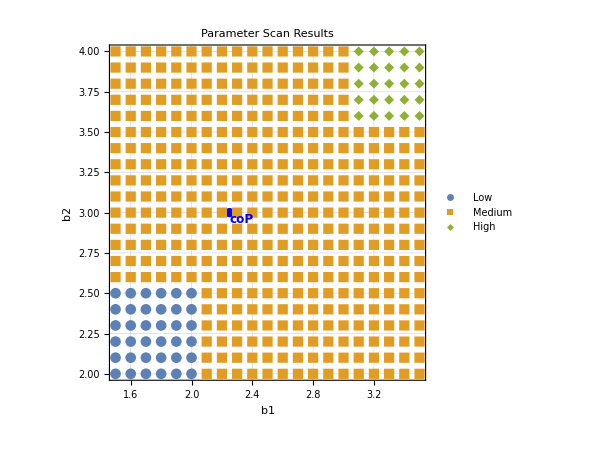

```mathematica
plot=scanPR[RHS,var,par,coP,{1.5,3.5},{2,4}]
```

```mathematica
(*If b1 and b2 are the 1st and 2nd parameters in par*)

plotInd={3,4};
scanPR[RHS,var,par,coP,plotInd,R01,R02,R21,R12]
```

Center values: b1 = HopfE`Private`b1, b2 = HopfE`Private`b2

Range::range: Range specification in Range[b2,1/(g2+m2),0.1] does not have appropriate bounds.

Range::range: Range specification in Range[0.5 HopfE`Private`b2,1.5 HopfE`Private`b2,0.1] does not have appropriate bounds.

Scanning 3 × 3 = 9 parameter combinations...

Range::range: Range specification in Range[Which[b2≤0.8 HopfE`Private`b1&&0.5 HopfE`Private`b2≤0.8 HopfE`Private`b2,Low,b2>1.2 HopfE`Private`b1N$9576&&0.5 HopfE`Private`b2>1.2 HopfE`Private`b2N$9576,High,True,Medium],Which[«1»],Which[b2≤0.8 HopfE`Private`b1&&0.1≤0.8 HopfE`Private`b2,Low,b2>1.2 HopfE`Private`b1N$9576&&0.1>1.2 HopfE`Private`b2N$9576,High,True,Medium]] does not have appropriate bounds.

General::stop: Further output of Range::range will be suppressed during this calculation.

General::prng: Value of option PlotRange -> {(b2 (g2+m2+a2 Λ))/((g2+m2) (b2+a2 μ)),{0.5 HopfE`Private`b2,1.5 HopfE`Private`b2}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ContourPlot::plln: Limiting value b2 in {HopfE`Private`b1,b2,1/(g2+m2)} is not a machine-sized real number.

General::stop: Further output of ContourPlot::plln will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in «1».

Show[-Graphics-,ContourPlot[Evaluate[{3,4}/.HopfE`Private`coPSubstituted$9576]==1,{HopfE`Private`b1,HopfE`Private`actualRangeB1$9576⟦1⟧,HopfE`Private`actualRangeB1$9576⟦2⟧},{HopfE`Private`b2,HopfE`Private`actualRangeB2$9576⟦1⟧,HopfE`Private`actualRangeB2$9576⟦2⟧},ContourStyle→Directive[Red,Thick],PlotPoints→50],ContourPlot[Evaluate[(b2 Λ)/((g2+m2) μ)/.HopfE`Private`coPSubstituted$9576]==1,{HopfE`Private`b1,HopfE`Private`actualRangeB1$9576⟦1⟧,HopfE`Private`actualRangeB1$9576⟦2⟧},{HopfE`Private`b2,HopfE`Private`actualRangeB2$9576⟦1⟧,HopfE`Private`actualRangeB2$9576⟦2⟧},ContourStyle→Directive[Blue,Thick],PlotPoints→50],ContourPlot[Evaluate[(b1 Λ)/((g1+m1) μ)/.HopfE`Private`coPSubstituted$9576]==1,{HopfE`Private`b1,HopfE`Private`actualRangeB1$9576⟦1⟧,HopfE`Private`actualRangeB1$9576⟦2⟧},{HopfE`Private`b2,HopfE`Private`actualRangeB2$9576⟦1⟧,HopfE`Private`actualRangeB2$9576⟦2⟧},ContourStyle→Directive[Green,Thick],PlotPoints→50],ContourPlot[Evaluate[(b1 (g1+m1+a1 Λ))/((g1+m1) (b1+a1 μ))/.HopfE`Private`coPSubstituted$9576]==1,{HopfE`Private`b1,HopfE`Private`actualRangeB1$9576⟦1⟧,HopfE`Private`actualRangeB1$9576⟦2⟧},{HopfE`Private`b2,HopfE`Private`actualRangeB2$9576⟦1⟧,HopfE`Private`actualRangeB2$9576⟦2⟧},ContourStyle→Directive[Orange,Thick],PlotPoints→50],-Graphics-,PlotLabel→Parameter Scan with Bifurcation Curves]

Scanning 64 points (wRan=0.5, hRan=0.5, hTol=0.01] for Hopf bifurcations...

Varying parameters at indices {3,4} with center values: {9/4,4}

Set::shape: Lists {HopfE`Private`posSols$10833,HopfE`Private`complexEigs$10833,HopfE`Private`eigs$10833} and {{},{},-90,{}} are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

Found 0 Hopf points

Show::gcomb: Could not combine the graphics objects in Show[Automatic,,PlotLabel→Parameter Scan: 0 Hopf Points Found,PlotRange→{{1.0125,3.7125},{1.8,6.6}}].

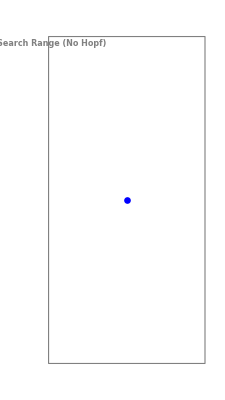
Show[Automatic,-Graphics-,PlotLabel→Parameter Scan: 0 Hopf Points Found,PlotRange→{{1.0125,3.7125},{1.8,6.6}}]

```mathematica
p0Val=par/.coP;
plotInd={3,4};
scanPar[RHS, var, par, p0Val, plotInd]
```

```mathematica
(*With custom step size*)
scanPR[RHS,var,par,coP,{1,2},R01,R02,R21,R12,Automatic,Automatic,0.05]

(*With custom ranges and step*)
scanPR[RHS,var,par,coP,{1,2},R01,R02,R21,R12,{1.0,3.0},{2.0,5.0},0.2]
```